## Setup

```mathematica
Clear["Global`*"];
```

```mathematica
LaunchKernels[6];
```

## Calculate T with forward difference method

### Manually integrate Schrodinger’s equation

The grid of x points in the region of the support of the potential

```mathematica
xgrid[p_]:=Module[{a,b,n,m, step,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n);

xs = Table[x,{x,a,b,step}]//N;

Return[xs];
]
```

The grid of x points in the entire region including some to the left of the support of the potential for determining the value of T.

```mathematica
xgridFull[p_]:=Module[{a,b,n,m, step,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n);

xs = Table[x,{x,a-m*step,b,step}]//N;

Return[xs];
]
```

The H-matrix which for the linear system to determine psi(x)

```mathematica
Hmat[V_, k_, p_]:=Module[{xg, a,b,n,m, step,xs, diag, u1, u2, mat, u1V, matV},
xg=xgrid[p];
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

(*Some of these elements are constant and should not be recreated for every solution *)
diag = Band[{1,1}]->1;
u1 = Band[{1,2}]->(-2+step^2*k^2);
u2=Band[{1,3}]->1;
mat = SparseArray[{diag,u1,u2},{1+n+m, 1+n+m}];

(*These elements are constant for every value of k and should only be generated once per k value*)
u1V=Band[{2,3}]->(-2*step^2*V[xg]);
matV = SparseArray[u1V,{1+n+m,1+n+m}];

Return[mat+matV];
];
```

The inhomogenous term for the linear system.

```mathematica
yvec[k_,p_]:=Module[{a,b,n,m, step,y},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n-1);

y =SparseArray[
{n+m->-1,n+m+1->(1-I*k*step-1/2*step^2*k^2)}, 
{n+m+1}];

Return[y];
]
```

Solve the linear system.

```mathematica
psiSoln[V_,k_,p_]:=
LinearSolve[Hmat[V,k,p],yvec[k,p],Method->"Banded"]
```

### Test with sech^2 potential

```mathematica
V[x_]:=1/Cosh[x]^2;
params = Association["a"->-10, "b"->10,"n"->1000,"m"->200];
```

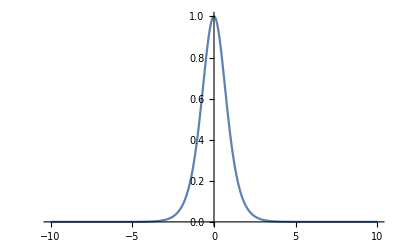

```mathematica
Plot[V[x],{x,params["a"],params["b"]},PlotRange->Full]
```

```mathematica
psiTest = psiSoln[V,3,params];
Length[psiTest]
```

1201

```mathematica
xGridFullTest = xgridFull[params];
Length[xGridFullTest]
```

1201

```mathematica
psiTestofX=Table[{xGridFullTest[[i]],psiTest[[i]]},{i,1,Length[psiTest]}];
```

```mathematica
pltWF=ListPlot[psiTestofX,GridLines->Automatic,PlotRange->{Automatic,{0,Automatic}}];
pltPot = Plot[V[x],{x,-14,10},PlotStyle->Red,PlotRange->Full];
```

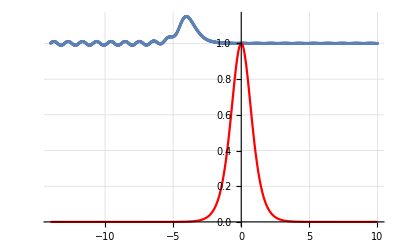

```mathematica
Show[pltWF,pltPot]
```

Test using schrodinger’s equation

```mathematica
psiTestInterp = Interpolation[psiTestofX]
```

InterpolatingFunction[{{-14., 10.}}, <>]

```mathematica
psiTestInterp[-3]
```

0.248021-0.994747 ⅈ

```mathematica
LogPlot[Abs[D[psiTestInterp[xp],{xp,2}][x]-(2*V[x]-3^2)*psiTestInterp[x]],{x,-12,10}]
```

-Graphics-

```mathematica
WaveFuncLeft[k0_]:=Module[{help=SchrEq[k0]},Fit[Table[Flatten[{x,f[x]/.help}],{x,a-c/k0,a,step/k0}],{Exp[I Sqrt[2]k0 x],Exp[-I Sqrt[2]k0 x]},x]];
```

```mathematica
(*Here we find the transmission coefficient -- it is determined by the coefficient in front of the incoming wave*)
```

```mathematica
T[k_]:=1/(WaveFuncLeft[k][[2]]/.x->0);
```

```mathematica
(*Now we check the solution using the exact result*)
```

```mathematica
t=Table[{k,Abs[T[k]]^2},{k,0.001,2,0.05}];
lp=ListPlot[t,PlotRange->All];
```

Table::iterb: Iterator {x,a-1000. c,a,1000. step} does not have appropriate bounds.

Fit::fitd: First argument Table[Flatten[{x,f[x]/.help$28877}],{x,a-1000. c,a,1000. step}] in Fit is not a list or a rectangular array.

Table::iterb: Iterator {x,a-19.6078 c,a,19.6078 step} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Fit::fitd: First argument Table[Flatten[{x,f[x]/.help$28884}],{x,a-19.6078 c,a,19.6078 step}] in Fit is not a list or a rectangular array.

Fit::fitd: First argument Table[Flatten[{x,f[x]/.help$28893}],{x,a-9.90099 c,a,9.90099 step}] in Fit is not a list or a rectangular array.

General::stop: Further output of Fit::fitd will be suppressed during this calculation.

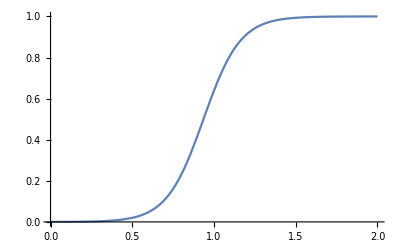

```mathematica
Show[Plot[Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2),{x,0,2}],lp]
```

## Comparing two methods

```mathematica
(*second method*)
```

```mathematica
Timing[Table[{k,Abs[T1[k]]^2},{k,0.001,2,0.01}]]
```

{0.35681,{{0.001,1.94358×10^-8},{0.011,2.35356×10^-6},{0.021,8.59561×10^-6},{0.031,0.0000187941},{0.041,0.0000330284},{0.051,0.0000514091},{0.061,0.0000740791},{0.071,0.000101215},{0.081,0.000133028},{0.091,0.000169766},{0.101,0.000211715},{0.111,0.000259203},{0.121,0.000312599},{0.131,0.000372321},{0.141,0.000438836},{0.151,0.000512663},{0.161,0.000594379},{0.171,0.000684624},{0.181,0.000784105},{0.191,0.0008936},{0.201,0.00101397},{0.211,0.00114615},{0.221,0.00129118},{0.231,0.00145019},{0.241,0.00162444},{0.251,0.00181527},{0.261,0.00202419},{0.271,0.00225283},{0.281,0.00250297},{0.291,0.00277656},{0.301,0.00307572},{0.311,0.00340279},{0.321,0.00376029},{0.331,0.004151},{0.341,0.00457793},{0.351,0.00504436},{0.361,0.00555388},{0.371,0.00611037},{0.381,0.00671808},{0.391,0.00738163},{0.401,0.00810602},{0.411,0.00889671},{0.421,0.0097596},{0.431,0.0107011},{0.441,0.0117282},{0.451,0.0128485},{0.461,0.01407},{0.471,0.0154017},{0.481,0.0168531},{0.491,0.0184345},{0.501,0.0201571},{0.511,0.0220328},{0.521,0.0240745},{0.531,0.0262962},{0.541,0.0287127},{0.551,0.0313398},{0.561,0.0341947},{0.571,0.0372955},{0.581,0.0406614},{0.591,0.0443131},{0.601,0.0482721},{0.611,0.0525614},{0.621,0.057205},{0.631,0.062228},{0.641,0.0676567},{0.651,0.0735181},{0.661,0.0798403},{0.671,0.0866519},{0.681,0.0939819},{0.691,0.10186},{0.701,0.110314},{0.711,0.119375},{0.721,0.129069},{0.731,0.139423},{0.741,0.150461},{0.751,0.162207},{0.761,0.174679},{0.771,0.187892},{0.781,0.201859},{0.791,0.216586},{0.801,0.232072},{0.811,0.248314},{0.821,0.265297},{0.831,0.283003},{0.841,0.301404},{0.851,0.320466},{0.861,0.340143},{0.871,0.360387},{0.881,0.381137},{0.891,0.402328},{0.901,0.423888},{0.911,0.445739},{0.921,0.4678},{0.931,0.489985},{0.941,0.512208},{0.951,0.53438},{0.961,0.556415},{0.971,0.578228},{0.981,0.599738},{0.991,0.620868},{1.001,0.641548},{1.011,0.661714},{1.021,0.681307},{1.031,0.700279},{1.041,0.718587},{1.051,0.736198},{1.061,0.753085},{1.071,0.76923},{1.081,0.784622},{1.091,0.799255},{1.101,0.813131},{1.111,0.826258},{1.121,0.838645},{1.131,0.850311},{1.141,0.861273},{1.151,0.871554},{1.161,0.881179},{1.171,0.890174},{1.181,0.898567},{1.191,0.906387},{1.201,0.913662},{1.211,0.920421},{1.221,0.926694},{1.231,0.932509},{1.241,0.937893},{1.251,0.942874},{1.261,0.947478},{1.271,0.95173},{1.281,0.955653},{1.291,0.95927},{1.301,0.962604},{1.311,0.965675},{1.321,0.968501},{1.331,0.971101},{1.341,0.973492},{1.351,0.97569},{1.361,0.977709},{1.371,0.979564},{1.381,0.981267},{1.391,0.982831},{1.401,0.984265},{1.411,0.985582},{1.421,0.98679},{1.431,0.987897},{1.441,0.988913},{1.451,0.989844},{1.461,0.990698},{1.471,0.991481},{1.481,0.992198},{1.491,0.992855},{1.501,0.993457},{1.511,0.994009},{1.521,0.994515},{1.531,0.994978},{1.541,0.995402},{1.551,0.995791},{1.561,0.996146},{1.571,0.996472},{1.581,0.996771},{1.591,0.997044},{1.601,0.997294},{1.611,0.997523},{1.621,0.997732},{1.631,0.997924},{1.641,0.9981},{1.651,0.99826},{1.661,0.998407},{1.671,0.998542},{1.681,0.998665},{1.691,0.998777},{1.701,0.99888},{1.711,0.998975},{1.721,0.999061},{1.731,0.99914},{1.741,0.999212},{1.751,0.999278},{1.761,0.999338},{1.771,0.999393},{1.781,0.999444},{1.791,0.99949},{1.801,0.999532},{1.811,0.999571},{1.821,0.999606},{1.831,0.999639},{1.841,0.999668},{1.851,0.999695},{1.861,0.99972},{1.871,0.999742},{1.881,0.999763},{1.891,0.999782},{1.901,0.9998},{1.911,0.999816},{1.921,0.99983},{1.931,0.999844},{1.941,0.999856},{1.951,0.999867},{1.961,0.999877},{1.971,0.999887},{1.981,0.999895},{1.991,0.999903}}}

```mathematica
(*first method*)
Timing[Table[{k,Abs[T[k]]^2},{k,0.001,2,0.01}]]
```

{0.455437,{{0.001,1.9381×10^-8},{0.011,2.34695×10^-6},{0.021,8.57174×10^-6},{0.031,0.0000187428},{0.041,0.0000329402},{0.051,0.0000512758},{0.061,0.000073894},{0.071,0.000100973},{0.081,0.000132726},{0.091,0.000169402},{0.101,0.000211292},{0.111,0.000258723},{0.121,0.00031207},{0.131,0.000371751},{0.141,0.000438236},{0.151,0.000512048},{0.161,0.000593766},{0.171,0.000684032},{0.181,0.000783554},{0.191,0.000893113},{0.201,0.00101357},{0.211,0.00114586},{0.221,0.00129103},{0.231,0.0014502},{0.241,0.00162463},{0.251,0.00181568},{0.261,0.00202482},{0.271,0.0022537},{0.281,0.00250409},{0.291,0.00277794},{0.301,0.00307737},{0.311,0.00340469},{0.321,0.00376244},{0.331,0.00415337},{0.341,0.00458049},{0.351,0.00504708},{0.361,0.0055567},{0.371,0.00611324},{0.381,0.00672094},{0.391,0.00738439},{0.401,0.00810861},{0.411,0.00889902},{0.421,0.00976155},{0.431,0.0107026},{0.441,0.0117292},{0.451,0.0128488},{0.461,0.0140696},{0.471,0.0154004},{0.481,0.0168509},{0.491,0.0184313},{0.501,0.0201529},{0.511,0.0220276},{0.521,0.0240683},{0.531,0.026289},{0.541,0.0287046},{0.551,0.031331},{0.561,0.0341853},{0.571,0.0372856},{0.581,0.0406514},{0.591,0.0443032},{0.601,0.0482627},{0.611,0.0525528},{0.621,0.0571975},{0.631,0.062222},{0.641,0.0676526},{0.651,0.0735163},{0.661,0.0798412},{0.671,0.0866558},{0.681,0.0939891},{0.691,0.10187},{0.701,0.110329},{0.711,0.119392},{0.721,0.12909},{0.731,0.139447},{0.741,0.150488},{0.751,0.162236},{0.761,0.174709},{0.771,0.187924},{0.781,0.201891},{0.791,0.216616},{0.801,0.232101},{0.811,0.248339},{0.821,0.265318},{0.831,0.283019},{0.841,0.301414},{0.851,0.320469},{0.861,0.34014},{0.871,0.360376},{0.881,0.381119},{0.891,0.402303},{0.901,0.423858},{0.911,0.445704},{0.921,0.467762},{0.931,0.489944},{0.941,0.512166},{0.951,0.534338},{0.961,0.556375},{0.971,0.578192},{0.981,0.599707},{0.991,0.620843},{1.001,0.64153},{1.011,0.661703},{1.021,0.681304},{1.031,0.700283},{1.041,0.718599},{1.051,0.736217},{1.061,0.75311},{1.071,0.76926},{1.081,0.784656},{1.091,0.799292},{1.101,0.813171},{1.111,0.826298},{1.121,0.838685},{1.131,0.850349},{1.141,0.861309},{1.151,0.871588},{1.161,0.881209},{1.171,0.890201},{1.181,0.89859},{1.191,0.906406},{1.201,0.913677},{1.211,0.920432},{1.221,0.926702},{1.231,0.932514},{1.241,0.937896},{1.251,0.942875},{1.261,0.947477},{1.271,0.951726},{1.281,0.955648},{1.291,0.959266},{1.301,0.9626},{1.311,0.96567},{1.321,0.968498},{1.331,0.971099},{1.341,0.973491},{1.351,0.97569},{1.361,0.977711},{1.371,0.979567},{1.381,0.981272},{1.391,0.982837},{1.401,0.984273},{1.411,0.985591},{1.421,0.9868},{1.431,0.987908},{1.441,0.988925},{1.451,0.989857},{1.461,0.990711},{1.471,0.991494},{1.481,0.992212},{1.491,0.992869},{1.501,0.993471},{1.511,0.994023},{1.521,0.994528},{1.531,0.994991},{1.541,0.995415},{1.551,0.995803},{1.561,0.996158},{1.571,0.996484},{1.581,0.996782},{1.591,0.997054},{1.601,0.997304},{1.611,0.997533},{1.621,0.997742},{1.631,0.997933},{1.641,0.998109},{1.651,0.998269},{1.661,0.998416},{1.671,0.99855},{1.681,0.998673},{1.691,0.998786},{1.701,0.998889},{1.711,0.998983},{1.721,0.999069},{1.731,0.999148},{1.741,0.99922},{1.751,0.999287},{1.761,0.999347},{1.771,0.999402},{1.781,0.999453},{1.791,0.999499},{1.801,0.999542},{1.811,0.999581},{1.821,0.999616},{1.831,0.999649},{1.841,0.999678},{1.851,0.999706},{1.861,0.99973},{1.871,0.999752},{1.881,0.999773},{1.891,0.999792},{1.901,0.999809},{1.911,0.999825},{1.921,0.99984},{1.931,0.999853},{1.941,0.999865},{1.951,0.999877},{1.961,0.999887},{1.971,0.999896},{1.981,0.999905},{1.991,0.999913}}}

## Just Fun)

```mathematica
V1[x_]:=1/Cosh[x-4]^2+1/Cosh[x+4]^2+0.5/Cosh[x]^2;
a1=-10;
b1=10;
c1=0.5;
SchrEq1[k0_]:=Module[{k=k0},
NDSolve[{-f''[x]/2+V1[x]f[x]-k^2 f[x]==0,f[b1]==Exp[I Sqrt[2]k b1],f'[b1]==I Sqrt[2] k Exp[I Sqrt[2] k b1]},f,{x,a1-c1,b1}]];
```

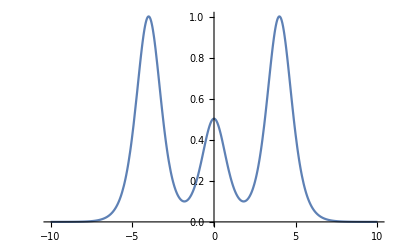

```mathematica
Plot[V1[x],{x,-10,10}]
```

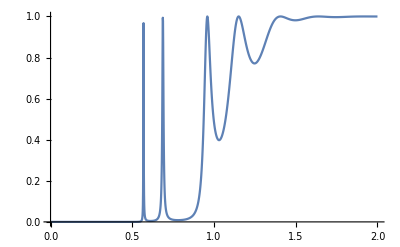

```mathematica
(*here we find the transmission coefficient from two points*)
T1[k0_]:=Module[{help=SchrEq1[k0]},(Exp[2Sqrt[2]I k0 a1]-Exp[2Sqrt[2]I k0 (a1-c1)])/(Exp[Sqrt[2]I k0 a1](f[a1]/.help)-Exp[Sqrt[2]I k0(a1-c1)](f[a1-c1]/.help))][[1]];

t1=Table[{k,Abs[T1[k]]^2},{k,0.001,2,0.001}];
lp1=ListPlot[t1,PlotRange->All,Joined->True];

Show[lp1]
```

## Packaging the above routines as a function of the potential

```mathematica
SEDict=Association["a"->-10, "b"->10, "c"->4];
```

```mathematica
SchrEqOfV[V_,VParams_,SEDict_,k_]:=Module[{a,b,c, sol},
a=SEDict["a"];
b=SEDict["b"];
c=SEDict["c"];

sol = NDSolve[{-f''[x]/2+V[x, VParams]f[x]-k^2 f[x]==0,f[b]==Exp[I Sqrt[2]k b],f'[b]==I Sqrt[2] k Exp[I Sqrt[2] k b]},f,{x,a-c/k,b}];
Return[sol];
];
```

```mathematica
VTest[x_,params_]:=Module[{a,b,c,pot},
(* Extract params*)
a=params[[1]];
b=params[[2]];
c=params[[3]];
(* Calculate potential *) 
pot = a/Cosh[(x-b)/c]^2;
Return[pot]
];
```

```mathematica
VParamsTest = {1,0,1};
```

```mathematica
func=(f/.SchrEqOfV[VTest, VParamsTest, SEDict,1][[1]])
```

InterpolatingFunction[{{-14., 10.}}, <>]

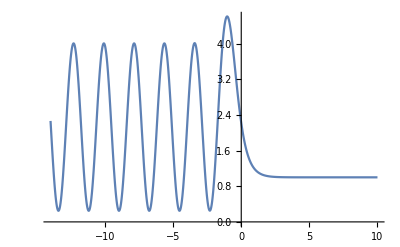

```mathematica
Plot[Abs[func[x]]^2,{x,-14,10}]
```

```mathematica
WaveFuncLeftOfV[V_, VParams_, SEDict_, k_,step_:1]:=Module[{a,b,c,help=SchrEqOfV[V,VParams,SEDict,k]},
a=SEDict["a"];
b=SEDict["b"];
c=SEDict["c"];
Fit[Table[Flatten[{x,f[x]/.help}],{x,a-c/k,a,step/k}],{Exp[I Sqrt[2]k x],Exp[-I Sqrt[2]k x]},x]
];
```

```mathematica
TofV[V_,VParams_, SEDict_,k_,step_:1]:=1/(WaveFuncLeftOfV[V, VParams,SEDict,k,step][[2]]/.x->0);
```

```mathematica
t=Table[{k,Abs[TofV[VTest, VParamsTest, SEDict, k]]^2},{k,0.001,2,0.01}];
lp=ListPlot[t,PlotRange->All];
```

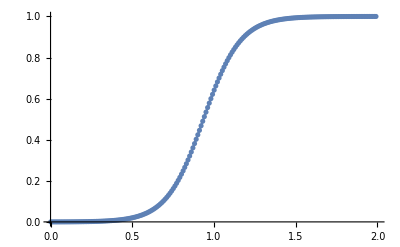

```mathematica
Show[Plot[Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2),{x,0,2}],lp]
```

## Timing

```mathematica
res = ParallelTable[{k,Abs[TofV[VTest, VParamsTest, SEDict, k]]^2},{k,0.001,2,0.001}]//Timing;
```

```mathematica
res[[1]] (*seconds*)
```

0.426094

```mathematica
Length[res[[2]]]
```

2000

```mathematica
(*SE solutions per second*)
```

```mathematica
Length[res[[2]]]/res[[1]]
```

4693.8

## TofKVec

```mathematica
getKVec[kmin_,kmax_,knum_]:=Table[k,{k,kmin,kmax,(kmax-kmin)/(knum-1)}]
```

```mathematica
TofVVec[V_,VParams_,SEDict_,kVec_]:=ParallelTable[{k,TofV[V, VParams, SEDict, k]},{k,kVec}]
```

```mathematica
kVecTest=getKVec[0.01,2,100];
```

## Cost

```mathematica
Cost[T_, TGoal_, weights_:Table[1,{i,1,Length[T_]}]]:=
Module[{Tdiff, cost},
(*Calculate difference in vectors*)
Tdiff=Table[{T[[i,1]],Abs[T[[i,2]]-TGoal[[i,2]]]^2},{i,1,Length[T]}];

(*Calculate loss. Estimate integral using midpoint rule. Normalize by interval. *)
cost = Sum[(Tdiff[[i+1,1]]-Tdiff[[i,1]]) * 1/2 * (weights[[i]]*Tdiff[[i,2]]+weights[[i+1]]*Tdiff[[i+1,2]]),{i,1,Length[T]-1}] / Sum[(Tdiff[[i+1,1]]-Tdiff[[i,1]]) * 1/2 * (weights[[i]]+weights[[i+1]]),{i,1,Length[T]-1}];
Return[cost];
];
```

```mathematica
TGoalTest=Table[{x,Sqrt[Sinh[Pi Sqrt[2]x]^2/(Sinh[Pi Sqrt[2]x]^2+Cosh[Pi Sqrt[7]/2]^2)]},{x,kVecTest}];
```

```mathematica
(* Plot the cost as a function of "a=1+eps", the coefficient of the Sech^2 potential. "eps=0" should reproduce the analytic results. *)
(* Getting lots of errors here, but the plot works fine. May have to worry more about these in the NMinimize routine. *)
ListPlot[Table[{eps,Cost[Abs[TofVVec[VTest,{1+eps,0,1},SEDict,kVecTest]],TGoalTest]},{eps,-0.5,0.5,1/19}]]
```

Part::partw: Part 3 of {1,1} does not exist.

Part::partw: Part 4 of {1,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

## Differential Evolution

```mathematica
(* Minimize the parameters of the potential to find the known solution. *)
```

```mathematica
(*NMinimize[{Hold[Cost[Abs[TofVVec[VTest,{v1,0,v3},SEDict,kVecTest]], TGoalTest]],{v3>0}},{v1,v3}, 
Method->{"DifferentialEvolution", "Tolerance"->0.02}, 
AccuracyGoal->2,
PrecisionGoal->2,
StepMonitor:>Hold[Print["Params: ",{v1,0,v3} , " Cost: ", Cost[Abs[TofVVec[VTest,{v1,0,v3},SEDict,kVecTest]], TGoalTest]]]]*)
```

## Gaussian Potential

```mathematica
VGauss[x_,params_]:=Module[{pot,A,x0,sigma},
A=params[[1]];
x0=params[[2]];
sigma=params[[3]];

pot = A*Exp[-(x-x0)^2/2/sigma];

Return[pot];
];
```

```mathematica
VGaussN[x_,params_]:=Module[{pot},
pot=Sum[VGauss[x,pars],{pars,params}];
Return[pot];
];
```

{{-1,-0.5,0.7},{0.5,0.5,1.5}}

0.5 ⅇ^(-0.333333 (-0.5+x)^2)-ⅇ^(-0.714286 (0.5+x)^2)

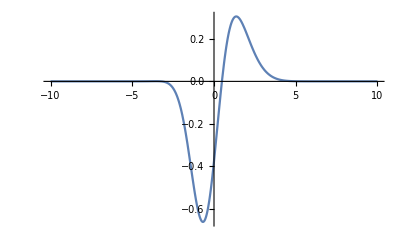

```mathematica
paramsTest = {{-1,-0.5,0.7},{0.5,0.5,1.5}}
VGaussN[x,paramsTest]
Plot[VGaussN[x,paramsTest],{x,a,b},PlotRange->All]
```

```mathematica
(*solGaussN=NMinimize[{
Hold[Cost[Abs[TofVVec[VGaussN, {{A1,x01,sigma1},{A2,x02,sigma2}},SEDict,kVecTest]], TGoalTest]],
{sigma1>0.01,sigma2>0.01,x01+x02==0}
},
{A1,x01,sigma1,A2,x02,sigma2}, 
Method->{"DifferentialEvolution", "Tolerance"->0.001,"PostProcess"->False}, 
AccuracyGoal->2,
PrecisionGoal->2,
StepMonitor:> Hold[Print["Params: ",{A1,x01,sigma1,A2,x02,sigma2} , " Cost: ", Cost[Abs[TofVVec[VGaussN, {{A1,x01,sigma1},{A2,x02,sigma2}},SEDict,kVecTest]], TGoalTest]]]]*)
```

## A function to search for a potential which minimizes for a given TGoal

```mathematica
BackgroundWeights[k_]:=Sqrt[Sinh[Pi Sqrt[2]k]^2/(Sinh[Pi Sqrt[2]k]^2+Cosh[Pi Sqrt[7]/2]^2)]
```

```mathematica
CustomStepMonitor[TGoal_,Vfunc_,Vpars_,SEDict_,kVec_ ,weights_:Table[1,{i,1,Length[TGoal_]}]]:=Module[{PlotA,PlotB},
Print["Cost: ", Cost[Abs[TofVVec[Vfunc, Vpars,SEDict,kVec]], TGoal, weights]];
Print["Params: ",Vpars]; 

PlotA=Plot[Vfunc[x,Vpars],{x,SEDict["a"],SEDict["b"]},PlotRange->All];
PlotB=ListPlot[{TGoal,Abs[TofVVec[Vfunc, Vpars,SEDict,kVec]]},PlotRange->All];

(*Print both plots. Magic from mathematica stackexchange: https://mathematica.stackexchange.com/questions/80224/use-a-module-to-return-multiple-plots*)
CellPrint@ExpressionCell[#,"Output"]&/@{PlotA,PlotB};
]
```

```mathematica
SearchPotential [
TGoal_,Vfunc_,Vpars_,parConstrs_,SEDict_,kVec_, 
weights_:Table[1,{i,1,Length[TGoal_]}],
method_:{"DifferentialEvolution", "Tolerance"->0.001,"PostProcess"->True, "ScalingFactor"->0.75, "CrossProbability"->0.5}
]:=
Module[{VparsFlat, soln},
VparsFlat=Flatten[Vpars];
soln=NMinimize[{
Hold[Cost[Abs[TofVVec[Vfunc, Vpars,SEDict,kVec]], TGoal,weights]],
parConstrs
},
VparsFlat, 
Method->method, 
AccuracyGoal->2,
PrecisionGoal->2,
StepMonitor:> Hold[Catch[CustomStepMonitor[TGoal, Vfunc,Vpars,SEDict,kVec,weights]]]
];

Return[soln];
]
```

## “Low pass quantum filter”

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[0.5-k]},{k,kVecTest}];
```

```mathematica
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kVecTest}]
```

{0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25}

```mathematica
(*SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2}},
{sigma1>0.01,sigma2>0.01,x01+x02==0, x02≥0},
SEDict,
kVecTest,
weightsofKGoalCool]*)
```

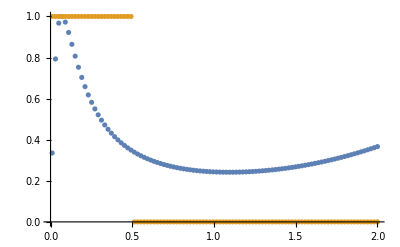

```mathematica
ListPlot[{Abs[TofVVec[VGaussN, {{-20.7882864835853,-9.77648183724065*^-7,0.40488075993662187},{29.8135962024409,9.77648183724065*^-7,0.09917420723971285}},SEDict,kVecTest]],TofKGoalCool}]
```

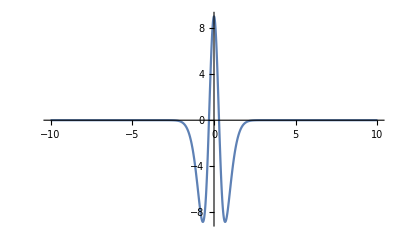

```mathematica
Plot[VGaussN[x,{{-20.7882864835853,-9.77648183724065*^-7,0.40488075993662187},{29.8135962024409,9.77648183724065*^-7,0.09917420723971285}}],{x,a,b},PlotRange->Full]
```

## “High-pass quantum filter”

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[k-0.5]},{k,kVecTest}];
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kVecTest}]
```

{0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25}

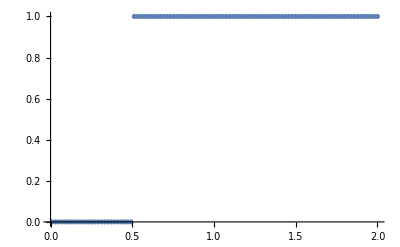

```mathematica
ListPlot[TofKGoalCool]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2}},
{sigma1>0.01,sigma2>0.01,x01+x02==0, x02≥0},
SEDict,
kVecTest]*)
```

## “Low-pass quantum filter” 3 gaussians

```mathematica
TofKGoalCool=Table[{k,HeavisideTheta[-k+0.5]},{k,kVecTest}];
weightsofKGoalCool=Table[(1-0.5/2)*HeavisideTheta[-k+0.5]+0.5/2*HeavisideTheta[k-0.5],{k,kVecTest}]
```

{0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.75,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25}

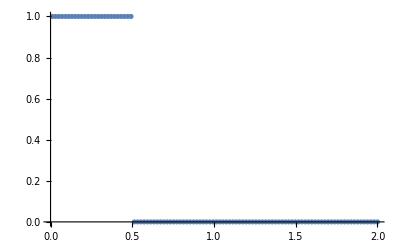

```mathematica
ListPlot[{TofKGoalCool}]
```

```mathematica
(*solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2},{A3,x03,sigma3}},
{sigma1>0.01,sigma2>0.01,sigma3>0.01,x01+x02+x03==0},
SEDict,
kVecTest,
weightsofKGoalCool]*)
```

## “k=1 comb” 3 gaussians

```mathematica
TofKGoalCool=Table[{k,KroneckerDelta[k,kVecTest[[Round[Length[kVecTest]/2]]]]},{k,kVecTest}];
weightsofKGoalCool=Log[1+Table[(1+(Length[kVecTest]-1)*KroneckerDelta[k,kVecTest[[Round[Length[kVecTest]/2]]]])*BackgroundWeights[k],{k,kVecTest}]]^2
```

{1.93667×10^-6,0.0000175912,0.00004931,0.0000979618,0.00016494,0.000252198,0.000362302,0.000498501,0.000664814,0.000866137,0.00110837,0.00139859,0.0017452,0.00215818,0.00264927,0.00323234,0.00392362,0.00474209,0.00570988,0.00685268,0.00820024,0.00978681,0.0116517,0.0138396,0.0164013,0.0193938,0.0228809,0.0269326,0.0316256,0.0370422,0.0432689,0.0503955,0.0585113,0.0677025,0.0780476,0.0896116,0.10244,0.116552,0.131934,0.148532,0.16625,0.184941,0.204417,0.224447,0.244767,0.265095,0.285146,0.304642,0.323337,19.2365,0.357527,0.372749,0.386623,0.399136,0.410311,0.420205,0.428897,0.436479,0.443054,0.448724,0.453593,0.457756,0.461304,0.46432,0.466876,0.469038,0.470864,0.472403,0.473699,0.474789,0.475706,0.476475,0.477121,0.477662,0.478116,0.478497,0.478815,0.479082,0.479306,0.479493,0.47965,0.479781,0.479891,0.479983,0.48006,0.480124,0.480178,0.480223,0.48026,0.480292,0.480318,0.48034,0.480359,0.480374,0.480387,0.480398,0.480407,0.480414,0.480421,0.480426}

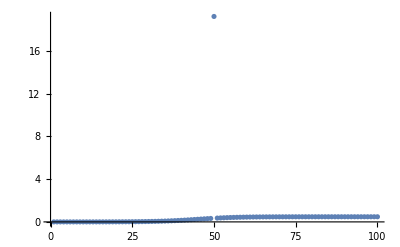

```mathematica
ListPlot[weightsofKGoalCool,PlotRange->All]
```

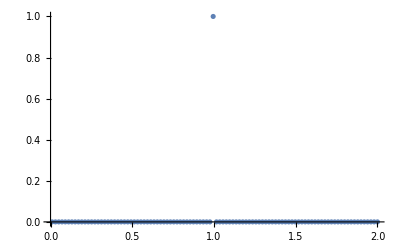

```mathematica
ListPlot[{TofKGoalCool}]
```

Cost: 0.513637

Params: {{0.990294,-0.280689,0.211788},{0.469454,0.280689,1.53754}}

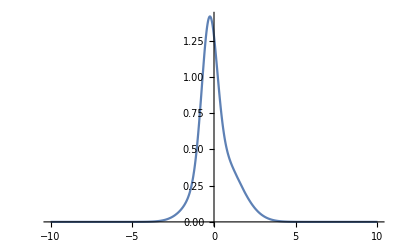

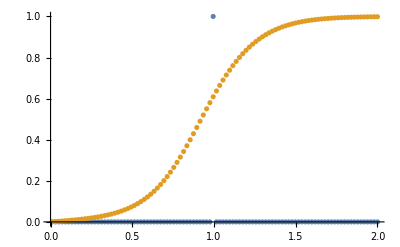

Cost: 0.481887

Params: {{1.58139,1.57296,0.12901},{-0.91253,-1.57296,1.21486}}

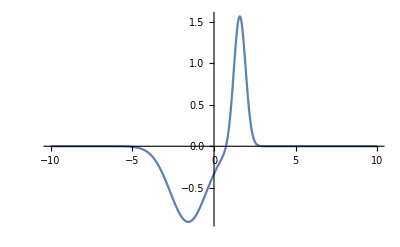

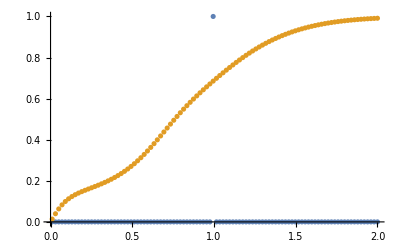

Cost: 0.481887

Params: {{1.58139,1.57296,0.12901},{-0.91253,-1.57296,1.21486}}

-Graphics-

-Graphics-

NMinimize::nnum: The function value 0.627963+2.37109 Max[1,Abs[Hold[Cost[Abs[TofVVec[VGaussN,{«2»},<|a→-10,b→10,c→4|>,{«100»}]],{«1»},{1.93667×10^-6,0.0000175912,0.00004931,0.0000979618,0.00016494,0.000252198,0.000362302,0.000498501,0.000664814,0.000866137,0.00110837,0.00139859,0.0017452,0.00215818,0.00264927,0.00323234,«19»,0.0896116,0.10244,0.116552,0.131934,0.148532,0.16625,0.184941,0.204417,0.224447,0.244767,0.265095,0.285146,0.304642,0.323337,19.2365,«50»}]]]] is not a number at {A1,A2,sigma1,sigma2,x01,x02} = {-0.0299187,2.53372,0.306003,1.344,0.872838,-0.872838}.

{0.481887,{A1→1.58139,A2→-0.91253,sigma1→0.12901,sigma2→1.21486,x01→1.57296,x02→-1.57296}}

```mathematica
solGaussN=
SearchPotential [
TofKGoalCool,
VGaussN,
{{A1,x01,sigma1},{A2,x02,sigma2}},
{sigma1>0.01,
sigma2>0.01, 
x01+x02==0, 
x01 <=SEDict["b"]-3*A1*sigma1,
x02 <=SEDict["b"]-3*A2*sigma2,
x01 >=SEDict["a"]+3*A1*sigma1,
x02 >=SEDict["a"]+3*A2*sigma2},
SEDict,
kVecTest,
weightsofKGoalCool]
```